# FaizonZaman/LexicalCases

Extract lexical patterns from text

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"Documentation"

"English"

"Guides"

"LexicalCases.nb"Documentation/English/Guides/LexicalCases.nb

"ReferencePages"

"Symbols"

"BoundToken.nb"Documentation/English/ReferencePages/Symbols/BoundToken.nb

"CountSummaryLowercase.nb"Documentation/English/ReferencePages/Symbols/CountSummaryLowercase.nb

"ExpandPattern.nb"Documentation/English/ReferencePages/Symbols/ExpandPattern.nb

"LexicalCases.nb"Documentation/English/ReferencePages/Symbols/LexicalCases.nb

"LexicalDispersionPlot.nb"Documentation/English/ReferencePages/Symbols/LexicalDispersionPlot.nb

"LexicalPattern.nb"Documentation/English/ReferencePages/Symbols/LexicalPattern.nb

"LexicalStructure.nb"Documentation/English/ReferencePages/Symbols/LexicalStructure.nb

"LexicalSummary.nb"Documentation/English/ReferencePages/Symbols/LexicalSummary.nb

"OptionalToken.nb"Documentation/English/ReferencePages/Symbols/OptionalToken.nb

"Sandwich.nb"Documentation/English/ReferencePages/Symbols/Sandwich.nb

"TextType.nb"Documentation/English/ReferencePages/Symbols/TextType.nb

"ToLexicalPattern.nb"Documentation/English/ReferencePages/Symbols/ToLexicalPattern.nb

"WordToken.nb"Documentation/English/ReferencePages/Symbols/WordToken.nb

"$LexicalCasesServices.nb"Documentation/English/ReferencePages/Symbols/$LexicalCasesServices.nb

"Tutorials"

"LexicalCasesOverview.nb"Documentation/English/Tutorials/LexicalCasesOverview.nb

"Kernel"

"LexicalCases.wl"Kernel/LexicalCases.wl

"LexicalPattern.wl"Kernel/LexicalPattern.wl

"Plots.wl"Kernel/Plots.wl

"Samples.wl"Kernel/Samples.wl

"Utilities.wl"Kernel/Utilities.wl

"Validation.wl"Kernel/Validation.wl

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

"Tests"

"LexicalCases.wlt"Tests/LexicalCases.wlt

"LexicalStructure.wlt"Tests/LexicalStructure.wlt

"Patterns.wlt"Tests/Patterns.wlt

"Utilities.wlt"Tests/Utilities.wlt

"Validation.wlt"Tests/Validation.wlt

## Web Content

### Headline Image

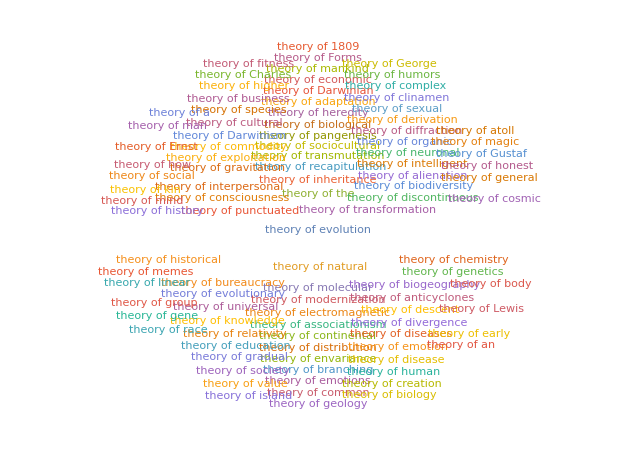

### Basic Description

Search text for lexical patterns. While similar to StringCases, TextCases etc., content types can be used freely in a StringExpression (as opposed to expressing complex lexical patterns in a Containing wrapper). Files, search index objects, and Wikipedia queries are supported. Results are returned in a summary object which supports several subvalues. Consult the documentation for usage.

### Details

I developed this functionality for a particular work task (Lexical Programmer @ Wolfram|Alpha). I needed to find adjectives that precede certain phrases. I started by gathering article text from Wikipedia of relevant domains, then searched for the desired lexical sequences. The initial approach used TextCases and TextContents with the Containing wrapper, (Containing["AdjectivePhrase",Verbatim["music"]] for example), but it was slow. So I designed some lexical tokens I could use in a StringExpression that could be used with StringCases.

TextCases is used internally to extract examples of a content type from the source text. These examples then replace the TextType in the StringExpression. You can see the lexical pattern generated from a piece of text with ExpandPattern. Note that this means, for example, if you have TextType["Adjective"] in your lexical pattern, the token will be replaced by all text snippets identified as adjectives in the source text.

I’d also like to say thanks to Swastik Banerjee for helping me improve SearchIndexObject support!

### Main Guide Page

File[FileNameJoin[{NotebookDirectory[],"Documentation","English","Guides","LexicalCases.nb"}]]

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[];
```

### Basic Examples

Search for verb phrases beginning with "Alice" in "Alice in Wonderland":

```mathematica
alice=ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
aliceVbAvb=LexicalCases[alice,"Alice"~~TextType["Verb"]~~TextType["Adverb"]]
```

LexicalSummary[…]

```mathematica
aliceVbAvb["Dataset"]
```

-Graphics-

```mathematica
aliceVbAvb["CountGroups"]
```

-Graphics-

### Scope

Search for a lexical pattern in Wikipedia articles containing "darwin":

```mathematica
darwin=LexicalCases["Content"->"darwin",BoundToken["theory of"]~~WordToken[1],MaxItems->1000];
```

```mathematica
darwin["CountGroups"]
```

-Graphics-

Search over index objects:

```mathematica
index = CreateSearchIndex["ExampleData/Text"]
```

SearchIndexObject[…]

```mathematica
indexResults=LexicalCases[index->All, WordToken[1]~~TextType["Verb"]];
```

Visualize the results in a WordCloud:

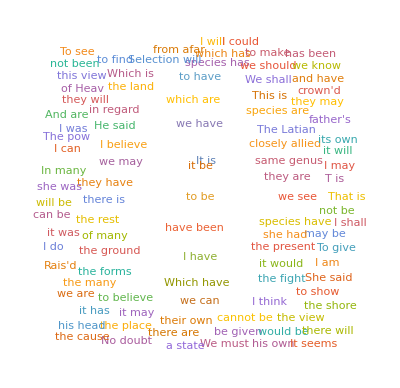

```mathematica
indexResults["WordCloud"]
```

## Source & Additional Information

### Creator

Faizon Zaman

### Source Control Repository

https://github.com/dishmint/LexicalCases

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

lexical cases

string cases

string search

text search

text cases

search

text analysis

text pattern

text pattern matching

pattern matching

lexical pattern

lexical patterns

linguistics

text mining

lexical dispersion

text dispersion

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

### Disclosures

DisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more informationLocal files

DisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more informationWolfram account

DisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more informationExternal services

DisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates, modifies or deletes symbols outside of the Publisher`PacletBaseName` context
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more informationWL system configuration

DisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more informationOS configuration

DisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more informationLocal system interactions

DisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more informationOther

## Author Notes

I’m a Lexical Programmer at Wolfram|Alpha and began developing this functionality for a particular work task. I needed to look at adjectives that precede certain phrases, so I gathered article text from Wikipedia of relevant domains, then searched for the desired lexical sequences. I initially tried using TextCases and TextContents with the Containing wrapper, (Containing["AdjectivePhrase",Verbatim["music"]] for example), but it was slow. So I designed some lexical tokens I could use in a StringExpression to perform lexical searches with StringCases.

Also, thanks to Swastik Banerjee for helping improve SearchIndexObject support.